```mathematica
(* Taylor polynomial at x=1/2 *)
```

```mathematica
Normal[Series[Sin[Pi x],{x,1/2, 2}]]//HornerForm
%//N
```

1-π^2/8+x (π^2/2-(π^2 x)/2)

-0.233701+(4.9348-4.9348 x) x

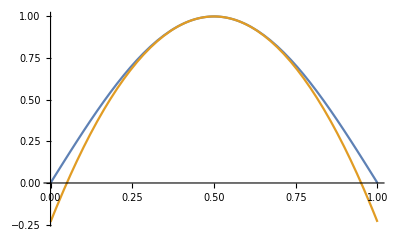

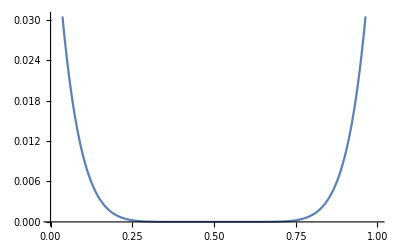

0.00625361

```mathematica
Plot[{Sin[Pi x],1-1/2 π^2 (x-1/2)^2},{x,0,1}]
Plot[(Sin[Pi x]-(1-1/2 π^2 (x-1/2)^2))^2,{x,0,1}]
Integrate[(Sin[Pi x]-(1-1/2 π^2 (x-1/2)^2))^2,{x,0,1}]//N
```

```mathematica
(* Lagrange polynomial using x=0, 1/2, 1 *)
```

```mathematica
xs:={0, 1/2, 1}
L0[x_]:=(x-xs[[2]])*(x-xs[[3]])/((xs[[1]]-xs[[2]])*(xs[[1]]-xs[[3]]))
L1[x_]:=(x-xs[[1]])*(x-xs[[3]])/((xs[[2]]-xs[[1]])*(xs[[2]]-xs[[3]]))
L2[x_]:=(x-xs[[1]])*(x-xs[[2]])/((xs[[3]]-xs[[1]])*(xs[[3]]-xs[[2]]))
P[x_]:=Sin[Pi xs[[1]]]*L0[x] + Sin[Pi xs[[2]]]*L1[x] + Sin[Pi xs[[3]]]*L2[x]
P[x]//Expand
```

4 x-4 x^2

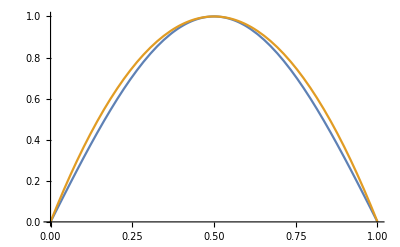

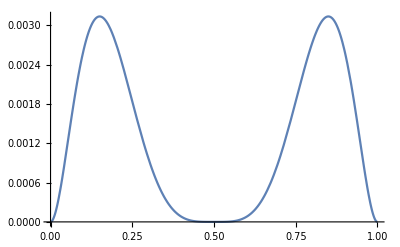

0.00128423

```mathematica
Plot[{Sin[Pi x],P[x]},{x,0,1}]
Plot[(Sin[Pi x]-P[x])^2,{x,0,1}]
Integrate[(Sin[Pi x]-P[x])^2,{x,0,1}]//N
```

```mathematica
(* Least squares polynomial on [0, 1] *)
```

-120/π^3+12/π+x (720/π^3-60/π+(-720/π^3+60/π) x)

-0.0504655+(4.12251-4.12251 x) x

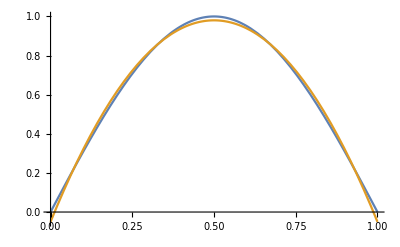

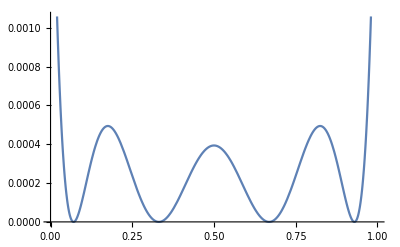

0.000298032

```mathematica
L[x_]:=-(720-60Pi^2)/Pi^3x^2+(720-60Pi^2)/Pi^3 x+(12Pi^2-120)/Pi^3
L[x]//HornerForm
%//N
Plot[{Sin[Pi x],L[x]},{x,0,1}]
Plot[(Sin[Pi x]-L[x])^2,{x,0,1}]
Integrate[(Sin[Pi x]-L[x])^2,{x,0,1}]//N
```

```mathematica
Solve[Sin[Pi x]==L[x],x, Reals]
```

{{x→Root[{120-12 π^2+π^3 Sin[π #1]-720 #1+60 π^2 #1+720 #1^2-60 π^2 #1^2&,0.070487993815798324094}]},{x→Root[{120-12 π^2+π^3 Sin[π #1]-720 #1+60 π^2 #1+720 #1^2-60 π^2 #1^2&,0.33141765608834597133}]},{x→Root[{120-12 π^2+π^3 Sin[π #1]-720 #1+60 π^2 #1+720 #1^2-60 π^2 #1^2&,0.66858234391165402867}]},{x→Root[{120-12 π^2+π^3 Sin[π #1]-720 #1+60 π^2 #1+720 #1^2-60 π^2 #1^2&,0.92951200618420167591}]}}

```mathematica
Cos[Pi*(k+1/2)/n]/.{k->0, n->2}//N
Cos[Pi*(k+1/2)/n]/.{k->1, n->2}//N
```

0.707107

-0.707107

```mathematica
Do[
a=Cos[Pi*(k+1/2)/n]/.{k->i, n->4};
Print[N[(a+1)/2]],{i,0,3}]
```

0.96194

0.691342

0.308658

0.0380602

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.